```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/student/compphys/week9

```mathematica
data=ReadList["!./pdf 100000",Number];
```

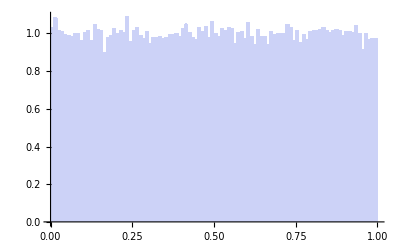

```mathematica
Histogram[data,100,"PDF"]
```

```mathematica
data=ReadList["!./pdf2 100000",Number];
```

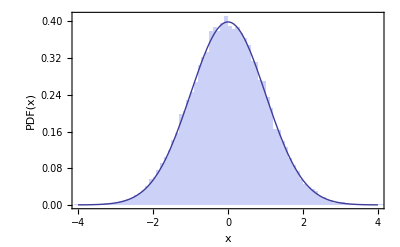

```mathematica
Show[Histogram[data,100,"PDF"],Plot[Exp[-x^2/2]/√(2π),{x,-4,4},PlotRange->All],Frame->True,PlotRange->{{-4,4},All},FrameLabel->{"x","PDF(x)"},BaseStyle->14]
```

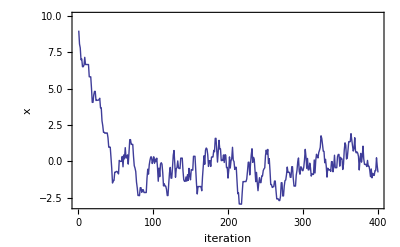

```mathematica
Block[{g},g=ListLinePlot[Table[{k,data[[k]]},{k,1,400,1}],PlotRange->{-3,10},Frame->True,FrameLabel->{"iteration","x"},BaseStyle->14];
Print[g];
Export["metro_normal_skip1.pdf",g];
]
```

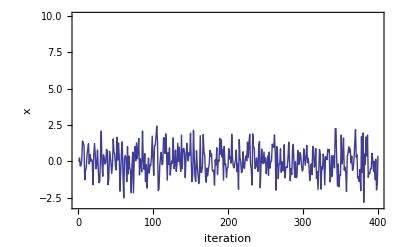

```mathematica
Block[{g},g=ListLinePlot[RandomVariate[NormalDistribution[],400],PlotRange->{-3,10},Frame->True,FrameLabel->{"iteration","x"},BaseStyle->14];
Print[g];
Export["indep_normal.pdf",g];
]
```

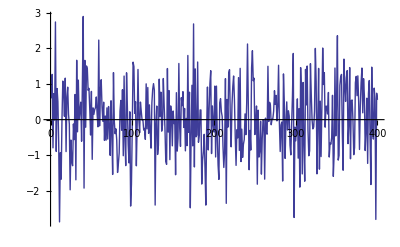

```mathematica
ListLinePlot[RandomVariate[NormalDistribution[],400]]
```

```mathematica
data=ReadList["!./pdf3 100000",Number];
```

```mathematica
zn=NIntegrate[Exp[-x^2/2]+Exp[-(x-8)^2/8],{x,-∞,∞}];
```

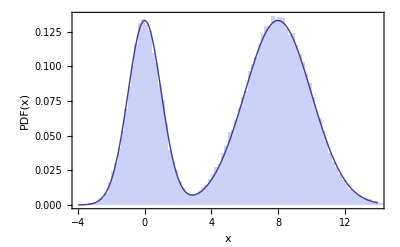

```mathematica
Show[Histogram[data,100,"PDF"],Plot[(Exp[-x^2/2]+Exp[-(x-8)^2/8])/zn,{x,-4,14},PlotRange->All],Frame->True,PlotRange->{{-4,14},All},FrameLabel->{"x","PDF(x)"},BaseStyle->14]
```

```mathematica
data=Partition[ReadList["!./gas 10 10 1 1 1 100000 4",Number],40];
```

```mathematica
data//Length
```

100

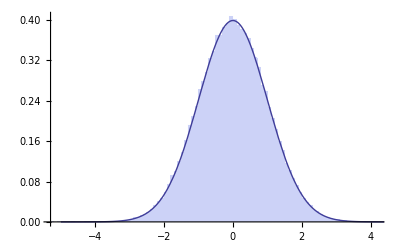

```mathematica
Show[Histogram[Flatten[data[[100;;,21;;]]],100,"PDF"],Plot[PDF[NormalDistribution[0,Sqrt[1.0]]][x],{x,-5,5}]]
```

```mathematica
ken[l_,n_]:=Total[l[[2n+1;;]]^2]/2
```

```mathematica
kendata=Table[ken[d,10],{d,data}];
```

```mathematica
Mean[kendata]
```

10.0128

```mathematica
StandardDeviation[kendata]/Sqrt[Length[kendata]]
```

0.00997292

```mathematica
bootstrap[list_,func_,tries_:100]:=Module[{meas},
meas=Table[func[RandomChoice[list,Length@list]],{tries}];
{Mean[meas],StandardDeviation[meas]}]
```

```mathematica
bootstrap[kendata,Mean]
```

{10.0135,0.0104884}

```mathematica
pot[l_,n_]:=Module[{v},
v[r_]:=4((1/r)^12-(1/r)^6);
Sum[v[Norm[l[[2*i-1;;2*i]]-l[[2*j-1;;2*j]]]],{i,n},{j,i+1,n}]]
```

```mathematica
potdata=Table[pot[d,10],{d,data}];
```

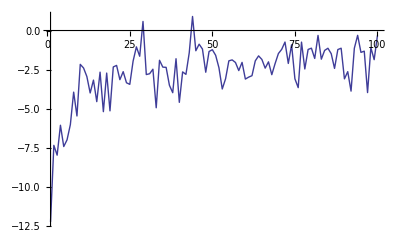

```mathematica
ListLinePlot[potdata[[;;100]],PlotRange->All]
```

```mathematica
show[l_,n_,L_]:=Graphics[{{FaceForm[],EdgeForm[Thick],Rectangle[{0,0},{L,L}]},{AbsolutePointSize[10],Table[Point[l[[2*i-1;;2*i]]],{i,n}]}}]
```

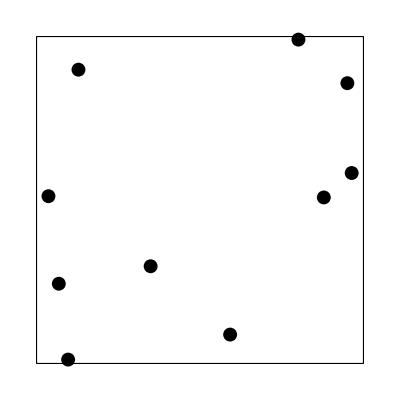

```mathematica
show[data[[1000]],10,10]
```

```mathematica
10 1/100.
```

0.1

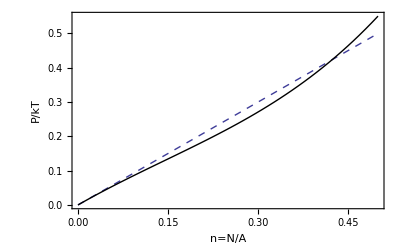

```mathematica
Plot[{x,x+-1.07347 x^2+2.427 x^3+0.25 x^4},{x,0,.5},Frame->True,FrameLabel->{"n=N/A","P/kT"},PlotStyle->{Dashed,Black}]
```

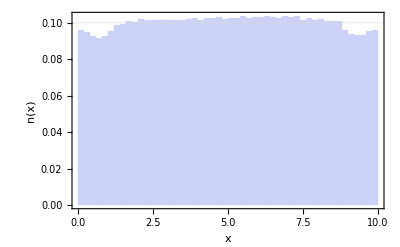

```mathematica
Block[{g},g=Histogram[Flatten[data[[100;;,;;20]]],30,"PDF",GridLines->{{},{.1}},Frame->True,FrameLabel->{"x","n(x)"},BaseStyle->14];
Print@g;
Export["density_profile.pdf",g];
]
```

```mathematica
Histogram[Flatten[data[[100;;,;;20]]],30,"PDF",GridLines->{{},{.1}},Frame->True,FrameLabel->{"x","n(x)"},BaseStyle->14]
```

-Graphics-

```mathematica
data[[1,;;20]]
```

{0.,0.,0.,1.12246,0.,2.24492,0.,3.36739,1.12246,0.,1.12246,1.12246,1.03609,2.42117,1.7352,4.65977,2.24492,0.,2.24492,1.12246}

```mathematica
closetowall[{x_,y_},L_,dx_]:=(x<dx)||(x>L-dx)||(y<dx)||(y>L-dx)
```

```mathematica
densvals=Table[Sum[If[closetowall[p,10,0.5],1,0],{p,Partition[data[[k,;;20]],2]}]/(4(10-0.5)0.5),{k,1,Length@data,10}];
```

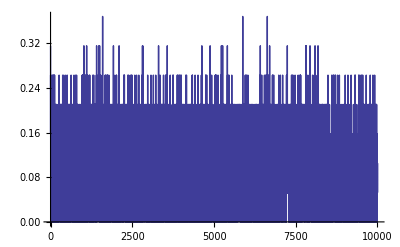

```mathematica
ListLinePlot[densvals]
```

```mathematica
bootstrap[densvals,Mean]
```

{0.0957286,0.000512719}

```mathematica
densvals=Table[Sum[If[closetowall[p,10,0.25],1,0],{p,Partition[data[[k,;;20]],2]}]/(4(10-0.25)0.25),{k,1,Length@data,10}];
```

```mathematica
bootstrap[densvals,Mean]
```

{0.0961775,0.00100179}

```mathematica
densvals=Table[Sum[If[closetowall[p,10,1.0],1,0],{p,Partition[data[[k,;;20]],2]}]/(4(10-1.0)1.0),{k,1,Length@data,10}];
```

```mathematica
bootstrap[densvals,Mean]
```

{0.0942629,0.000394897}

```mathematica
Needs["ErrorBarPlots`"]
```

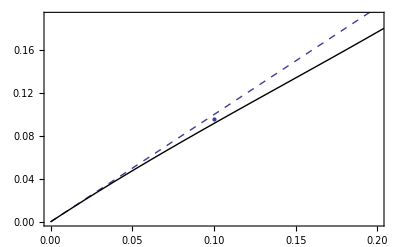

```mathematica
Show[ErrorListPlot[{{{.1,.0957},ErrorBar[.0005]}},Frame->True],Plot[{x,x+-1.07347 x^2+2.427 x^3+0.25 x^4},{x,0,.5},Frame->True,FrameLabel->{"n=N/A","P/kT"},PlotStyle->{Dashed,Black}]]
```

```mathematica
pressures=Block[{data,densvals},
Table[
{n/100,data=Partition[ReadList["out_N"<>ToString[n]<>"_L10.log",Number],4n];
densvals=Table[Sum[If[closetowall[p,10,0.5],1,0],{p,Partition[data[[k,;;2 n]],2]}]/(4(10-0.5)0.5),{k,1,Length@data,10}];
bootstrap[densvals,Mean]},{n,{5,10,15,20,25,30,35,40}}]
]
```

{{1/20,{0.0493079,0.00142822}},{1/10,{0.0994616,0.00197278}},{3/20,{0.140999,0.00211063}},{1/5,{0.184332,0.00259633}},{1/4,{0.225034,0.00289211}},{3/10,{0.272785,0.00284853}},{7/20,{0.328102,0.00350321}},{2/5,{0.383916,0.00347036}}}

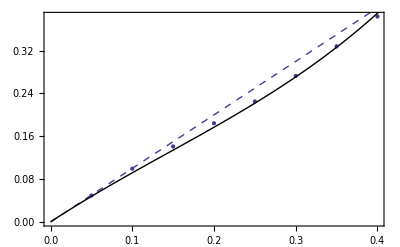

```mathematica
Show[ErrorListPlot[Table[{{d[[1]],d[[2,1]]},ErrorBar[d[[2,2]]]},{d,pressures}],Frame->True],Plot[{x,x+-1.07347 x^2+2.427 x^3+0.25 x^4},{x,0,.5},Frame->True,FrameLabel->{"n=N/A","P/kT"},PlotStyle->{Dashed,Black}]]
```